# Hydrogen atom

## Hands-on Mathematica Notebook

Giuseppe D’Auria

In this notebook we collect some definitions on the solution of radial equation for Hydrogen atom. We present some graphics examples for surfaces of equal probability and review some of the properties of the Laguerre polinomials;  in particular different conventions used in the literature are commented.

#### Packages and definitions

We protect a number of variables which are to be used as the global variables to prevent unwanted changes. The variables are those used in the options and a vector checkprobabilities which is used as a table.

```mathematica
Unprotect[plotφMax,plotscaled,plotφLines,plotminR,plotPoints,"checkprobabilities*"];
ClearAll["Global`*"];
Off[General::spell, General::spell1,InterpolatingFunction::"dmval"];
Protect[plotφMax,plotscaled,plotφLines,plotminR,plotPoints,"checkprobabilities*"];
```

## Definitions and conventions

The Schrödinger equation for a Coulomb (attractive) interaction between a nucleus of charge Ze and an electron of charge -e, V[r] = - Z e^2/ r, in radial coordinates, is

ℏ^2/(2m)(- 1/r^2∂/(∂r)(r^2∂/(∂r)ψ) + L^2/r^2 ψ) - (Z e^2)/r ψ = ℰ ψ

#### Units

All the dependence on Z, e, ℏ can be reabsorbed by a riscaling of variables, i.e. a change of units. Atomic units of length and energy (Bohr radius and atomic unit of energy) are defined as

a_B= ℏ^2/(m e^2) ≃ 0.529 ;  E_B = e^2/a_B= (m e^4)/ℏ^2≃ 4.36·10^-11erg = 27.21 eV.

Writing

r = a_B/Z ρ;  ℰ = Z^2 E_B ϵ ;

eq(EquationNumbered) becomes universal

-1/ρ^2∂/(∂ρ)(ρ^2∂/(∂ρ)ψ)+ L^2/ρ^2 ψ - 2/ρ ψ = 2 ϵ ψ.

In what follows we put r for ρ and ℰ for ϵ. Given a (normalized) solution of eq(EquationNumbered) the solution in usual units is obtained by substitution

ψ[r,θ,φ] ⟶  (Z/a_B)^(3/2) ψ[ (Z r)/a_B,θ,φ];                   ℰ ⟶ Z^2 E_B ℰ.

The overall factor takes care of the Jacobian from ρ to r variables in the normalization.

Relation (EquationNumbered) is very important: it relates different physical systems (with different Z) and gives at once the order of magnitude of the lengths and energy in a problem.

#### Separation of variables

L is the angular momentum (vector) operator. The Hamiltonian commutes with L^2 and L_z so the eigenstates can be written in the form

ψ_nLm[r,θ,φ] = R_nL[r] Y_Lm[θ,φ].

Y's are the spherical harmonics. Substituting in (EquationNumbered)  the equation for radial equation becomes (in natural units) and using the eigenvalue L(L+1) for L^2:

d^2/dr^2 R + 2/r d/dr R +(2 E + 2/r- (L(L+1))/r^2) R = 0

In the text it has been shown that normalized solutions of  (EquationNumbered) exist only for E = - 1/2 n^2 (energy eigenvalues), they are

R[n,L,r]= - 2/n^2 √(((n-L-1)!)/((n+L)!)^3)*((2 r)/n)^L * ⅇ^(-r/n)(ℒ_(n+L))^(2L+1)[2 r/n];

The functions ℒ are the Laguerre polynomials, and will be written below as ℒ[n+L,2L+1,2r/n]. The convention used for the Laguerre polynomials is not universal. In several Quantum Mechanics books, like Landau Lifchitz, the convention (EquationNumbered) is used, in other texts, and in particular in Mathematica and in the book of Abramowitz-Stegun, the notation is different

LaguerreL[n-L-1,2L+1,x] = - ℒ[n+L,2L+1,x]/((n+L)!).

In this notebook we will follow Mathematica convention, the relation between the two definitions is discussed below.

#### Radial functions

In natural units, as discussed above, the bound states radial eigenfunctions for Hydrogen atom are

```mathematica
R[ n_, L_,r_] :=  2/n^2 √(((n-L-1)!)/((n+L)!))((2 r)/n)^L  ⅇ^(-r/n) LaguerreL[n-L-1, 2 L + 1,(2 r)/n] ;
```

Allowed quantum numbers are

n = 1,2, ...  ;   L ≤ n-1;

```mathematica
TableForm[Table[Table[R[ n, L,r],{L,0,n-1}],{n,1,4}]]
```

2 ⅇ^-r |  |  | 
(ⅇ^(-r/2) (2-r))/(2 √2) | (ⅇ^(-r/2) r)/(2 √6) |  | 
(2 ⅇ^(-r/3) (27-18 r+2 r^2))/(81 √3) | 1/27 √(2/3) ⅇ^(-r/3) (4-(2 r)/3) r | 2/81 √(2/15) ⅇ^(-r/3) r^2 | 
1/768 ⅇ^(-r/4) (192-144 r+24 r^2-r^3) | (ⅇ^(-r/4) r (80-20 r+r^2))/(256 √15) | (ⅇ^(-r/4) (6-r/2) r^2)/(384 √5) | (ⅇ^(-r/4) r^3)/(768 √35)

Laguerre polynomials L_n^k(x) are polynomials of degree n, with n nodes, so the generic wave function R(n,L,r) has n-L-1 nodes. A graphical representation is given below

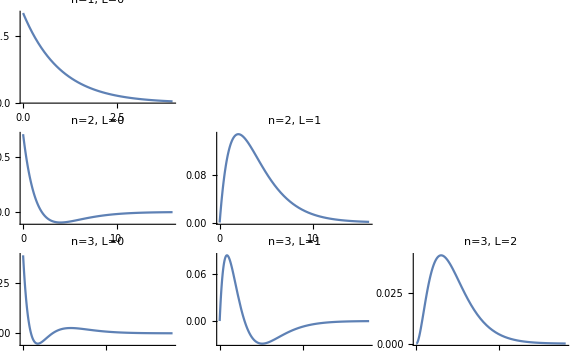

```mathematica
GraphicsGrid[ Table[Plot[R[n,L,r],{r,0,4 n^2},
PlotRange-> All,PlotLabel-> "n="<>ToString[n]<>", L="<>ToString[L]],{n,1,3},{L,0,n-1}],ImageSize-> 72 8]
```

## Graphical presentation

### 2D graphs

We plot the density |ψ_nLm|^2  on the plane (x,z). All the dependence on r is on the form r/n, where n is the principal quantum number. We take as variable the rescaled value  s = r/n, note that in this way graphs corresponding to different n are not on the same scale. For convenience we use unnormalized ψ. Using Y_L^m(θ,ϕ) ∝ P_L^m(cos(θ)) we write

```mathematica
ψ[n_,L_,m_,s_,θ_]:= (s)^L  ⅇ^(- s) LaguerreL[n-L-1, 2 L + 1,2 s]*LegendreP[L,Abs[m],Cos[θ]];
```

and for the relative probability

```mathematica
prob = Compile[{{n,_Integer},{L,_Integer},{m,_Integer},{ρ,_Real},{z,_Real}},
Evaluate[N@(ψ[n,L,m,√(ρ^2+z^2),ArcCos[z/√(ρ^2+z^2)]])^2]];
```

We have used cylindrical coordinates (ρ, z) and a compiled version for prob (See Mathematica Help for Compile).

We use DensityPlot[] for plotting.

```mathematica
rMax = 12; ϵ = 10^-8;
```

```mathematica
densityPsi[n_,L_,m_]:=
 DensityPlot[(aaVal=ψ[n,L,m,√(x^2+z^2),ArcCos[z/√(x^2+z^2)]]);aaVal*Conjugate[aaVal],{x,-rMax,rMax},{z,-rMax,rMax},
 ColorFunction->(Hue[0.2+ 0.2 #,0.7, #]&),
PlotPoints-> 15,MaxRecursion-> 4,
PerformanceGoal-> "Quality",ImageSize-> 72 4,
PlotLabel-> "n = "<>ToString[n]<> 
" L = "<>ToString[L]<>" m = "<>ToString[m]]
```

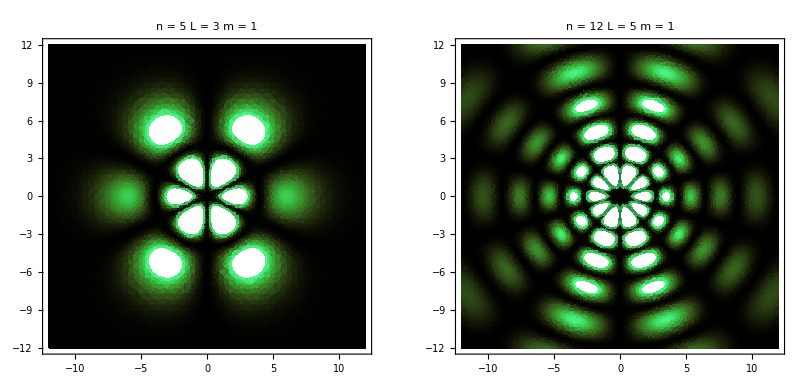

```mathematica
GraphicsGrid[{{densityPsi[5,3,1],densityPsi[12,5,1]}}]
```

### 3D graphs

There can be several possibilities for representing in 3D space the probability distribution. We choose to plot surfaces of equal probabilities. The normalization is given by the maximum of |ψ|^2 .

We are here only interested in eigenstates and these depend on azimuth φ only trough a phase, so we can  make a 3D plot of |ψ|^2 by rotating around z axis a contour plot in (x,z) plane. Of we can use directly Mathematica function ContourPlot3D.

Below we present three different options, ContourPlot3D, a function build3D which generate the surface rotating a two-dimensional contour and interpolating with polygons, an a third possibility, smoothbuild3D which is similar to build3D but instead of computing polygons use a Mathematica function to rotate the two dimensional contour.

The result of the three options is shown below, numbers show the CPU times on our computer for each method. We have to add that in last figure the two dimensional contour is generated with the option PlotPoints-> 75, with the same value for the option the second procedure take the same time.

23.3537
-Graphics3D-0.183618
-Graphics3D-1.45477
-Graphics3D-

#### Preliminaries

To simplify our task it is prefereable to have an estimate of the maximum of |ψ|^2 , that will be used to normalize the probabilities, and where approximatively the relative probability has a certain value. In the folowing p wil means relative probability. We assume to scan a  range c_i of (relative) probabilities from 1/40 = 0.025 to 1. We fix for the moment on the first 4 levels and construct a table maxProb[n,L,m] which contains the maximum of |ψ|^2 and a vector indicating approximatively the maximum radius where p ∼ c_i. This preliminary work is done taking a number pp of points along z and ρ, and computing there |ψ|^2.  The target probabilities are:

```mathematica
Unprotect["checkprobabilities*"];
checkprobabilities = Table[x,{x,0.025,1,0.025}];
Protect["checkprobabilities*"];
```

```mathematica
pointsSample = 50; rmaxSample=10.; ϵ = 10.^-8; nMax=4; numprobabilities = Length[checkprobabilities];
```

Here we construct the table. xP measure the radius of points where the relative probability has the desired value, dist take the maximum of these distances. A small complication arises because sometimes this probability is not reached in our sample, in these case dist gives -∞ as maximum and sdist select only meaningful distances. Possible holes (i.e. no good points) are filled with a simple interpolation (pip).

```mathematica
Table[
maxProb[n,L,m]= 
Module[{data,maxdata,dist,sdist,posdist,pip,Rmax,pp,R},
R = rmaxSample; pp = pointsSample;
data = Table[prob[n,L,m,ρ,z],{ρ,ϵ,R- ϵ,(R-ϵ)/pp},{z,0,R,R/pp}];
maxdata = Max[data];
 data = Round[numprobabilities*data/maxdata];
indPoints=Table[Position[data,k],{k,1,numprobabilities}];
xP=Table[
Norm[N[{(ϵ - (R-ϵ)/pp),-R/pp}]+{(R-ϵ)/pp,R/pp}*indPoints[[k]][[j]]],{k,1,Length[indPoints]},{j,1,Length[indPoints[[k]]]}];
dist=Max[#1]&/@xP;
sdist=Select[dist, #1>0&];
posdist=Flatten[(Position[dist,#1]&)/@ sdist];
pip=Interpolation[Transpose[{Flatten[posdist],Flatten[sdist]}],InterpolationOrder->2];
Rmax=Table[pip[k],{k,1,numprobabilities}];
{maxdata,Rmax}],{n,0,nMax},{L,0,n-1},{m,0,L}];//Timing
```

{0.21875,Null}

If a level not present in the tabel maxProb is requested we can write a function which do the same work, but now for a definite requested probability

```mathematica
newDatamaxProb[n_,L_,m_,probability_]:= Module[{data,md1,indPoints,xP,dist,sdist,pp,R},
R = rmaxSample; pp = pointsSample;
data = Table[prob[n,L,m,ρ,z],{ρ,ϵ,R- ϵ,(R-ϵ)/pp},{z,0,R,R/pp}];
md1 = Max[data];
 data = Round[1000*data/md1];
indPoints=Position[data,Floor[1000*probability]]; 
If[Length[indPoints]== 0,Return[{md1,{R/pp}}]]; 
xP=Table[
Norm[N[{(ϵ - (R-ϵ)/pp),-R/pp}]+{(R-ϵ)/pp,R/pp}*indPoints[[1]][[j]]],{j,1,Length[indPoints[[1]]]}];
dist=Max[#1]&/@xP;
(* Print["ecco dist  ",dist]; *)
sdist=Select[dist, #1>0&];
sdist = Max[sdist,R/pp];
{md1,{sdist}}]
```

#### Use ContourPlot3D

This is the simplest possibility.

```mathematica
useMath3D[{n_,L_,m_},prob_]:= Module[{norm,vecR1,R},
R=10;
{norm,vecR1}=If[n≤ nMax, maxProb[n,L,m],newDatamaxProb[n,L,m,prob]];
ContourPlot3D[1/norm*(N@ψ[n,L,m,√(x^2+y^2+z^2),ArcCos[z/√(x^2+y^2+z^2)]])^2 - prob == 0,
{x,-R,R},{y,-R,R},{z,-R,R},Boxed-> False,Axes-> False,Mesh-> None,PlotRange-> Automatic,ViewPoint->2{3,3,1}]]
```

```mathematica
useMath3D[{3,2,1},0.1]
```

You can rotate, zoom , copy etc. the above figure as any other 3d-graph. Explore with the mouse the various opportunities. To zoom use the key Alt and click with the mouse, shifting up will zoom, down will reduce the figure.

The reader can appreciate the beauty of the figure, but it take a relatively long  time to produce it. For smaller probabilities and other states, when the distribution becomes more complicated, to get the same quality i tis necessary to use the option PlotPoints-> 30, 50  or similar values. In this case the time grows of a factor 5. This is why we explore other possibilities.

#### Curve of revolution with polygons

The idea of the construction is borrowed from a book of M. Trott [*], and slightly modified. We can draw a two dimensional contour plot. This plot contains the lines of equal probabilities and we can extract them. Each line is essentially a list of points, here in 2d. We can insert a 0 for the y coordinate and consider these lines as lines in the 3d x-z plane. Now we can perform a small rotation of the line. If we consider a couple of points in the first line and the corresponding rotated couple, we can use the function Polygon to create a small polygon lying on the surface spanned in the small rotation. We iterate the procedure and obtain the whole surface.

For the a reader novice to Mathematica to follow the construction is a quite difficult task, and require some familiarity with the language. To help the interested reader we give below a short description of the code, otherwise you can limit yourself to the description of the use of this function.

To simplify the possible choices we give some arguments as options, which can be settled in the usual way option-> value. All these options can be omitted in usual cases.

```mathematica
Options[make3DPlotV6]={plotφMax-> 2Pi,plotscaled-> False,plotφLines-> 32,plotminR-> 0.5,,plotPoints-> Automatic};
```

Their meaning is

plotφMax  the angle you want to cover in the rotation, the default is 2π, but with 3π/2 you can "look inside" the surface.

plotscaled: the default is False, which means that the figure is plotted as bigger as possible (means PlotRange -> Automatic). If you want to compare the size of distributions for different probabilities you need a common scale, in this case put scaled True.

plotφlines: how many meridians you have in your plotφMax angle. Augmenting this parameter is good for graphics and bad for time.

plotminR: sometimes, for high excited levels, or some S-states, it can be necessary to have a minimum radius around which  looking for equipotential surfaces. Usually you do not need to change this parameter, almost unused in any case.

plotPoints; as plotminR you should not use this parameter, except for particular nasty graphs, tipically for very lows probabilities if you want finer details on the graph.

The function itself is make3DPlotV6. It requires as input a 3-vector with the quantum numbers and the requested probability. You can add, if you wish, some option taken from the above catalogue.

The 3 functions below, cfR, makePolygons, and lineTo3DSurfaceOfRevolution are function used inside make3DPlotV6. mycolor is just a color for the graph.

```mathematica
cfℛ=Compile[{{xyz,_Real,1},{ppφ,_Integer},φMax},Table[{{Cos[φ],Sin[φ],0.},{-Sin[φ],Cos[φ],0.},{0.,0.,1.}}.xyz,{φ,0,φMax,φMax/ppφ}]];
makePolygons[m_]:=Table[Polygon[{m[[i,j]],m[[i+1,j]],m[[i+1,j+1]],m[[i,j+1]]}],{i,Length[m]-1},{j,Length[m[[1]]]-1}];
lineTo3DSurfaceOfRevolution[Line[l_],φMax_,pp_]:=makePolygons[cfℛ[Insert[#,0,2],pp,φMax]&/@l]
```

```mathematica
mycolor=RGBColor[0.923079, 0.616144, 0.121675];
```

If a probability in the range described by checkprobabilities is requested the normalization and the approximate distance used in ContourPlot is obtained by the computed values maxProb[n,L,m], otherwise the parameters are computed with newDatamaxProb.  An instance in which this last feature is automatically used when very small probabilities for S waves are to be considered: in this case the distribution covers a wide range of r and finer structures appear.

```mathematica
make3DPlotV6[{n_,L_,m_},c_:.5,opts___]:=Module[
{lcp,lines,R,R1,norm,vecR1,RPlot,rangePlot,φMax,scaled,φLines,minR,myPlotPoints},
{φMax,scaled,φLines,minR,myPlotPoints}=
{plotφMax,plotscaled,plotφLines,plotminR,plotPoints}/.{opts}/.Options[make3DPlotV6];
(* *)
{norm,vecR1}=If[n≤ nMax && c≥  checkprobabilities[[1]],
 maxProb[n,L,m],newDatamaxProb[n,L,m,c]];
R =If[Length[vecR1]>1,Max[2.5vecR1[[Ceiling[Length[vecR1]*c]]],minR],
Max[1.2vecR1[[1]],minR]];
RPlot = Max[1.5*Max[vecR1],1.1R];
rangePlot=If[scaled== True,{{-RPlot,RPlot},{-RPlot,RPlot},{-RPlot,RPlot}},
Automatic];
 lcp= ContourPlot[1/norm(N@ψ[n,L,m,√(ρ^2+z^2),ArcCos[z/√(ρ^2+z^2)]])^2 - c == 0 ,{ρ,ϵ,R },{z,0,R},
(* PerformanceGoal-> "Quality", *)
(* PlotPoints-> myPlotPoints,*)
PlotPoints-> ControlActive[Automatic,myPlotPoints],
 ContourShading->False];  
lines = Cases[Normal[lcp],_Line,Infinity];
lines=Join[lines,lines/.Line[a_]:> Line[{1,-1}#&/@a]];
Graphics3D[{  EdgeForm[], 
 mycolor,Specularity[Orange,3.5], 
lineTo3DSurfaceOfRevolution[#,φMax,φLines]&/@lines},
PlotLabel-> "|ψ|^2 "<>ToString[{n,L,m}],
SphericalRegion->True, PlotRange-> rangePlot, Boxed->False]]
```

The graph for the same level (3, 2, 1) now tooks less then one hundred the previous time, the quality is not the same of course.

```mathematica
make3DPlotV6[{3,2,1},0.1]
```

It is now possible to construct tables for all levels, like the following, in a reasonable short time

```mathematica
GraphicsGrid[Table[make3DPlotV6[{4,L,m},0.2],{L,0,3},{m,0,L}],ImageSize-> 72 6]
```

A funny example which show the use of one option ( plotφMax ). You can rotate the graphs with the mouse.

```mathematica
GraphicsGrid[{{make3DPlotV6[{4,2,0},0.04],make3DPlotV6[{4,2,0},0.04,plotφMax-> 3π/2]}},
ImageSize-> 72 8]
```

#### Interactive graphics

It is easy to give an interactive version for make3DPlotV6, you need just to wrap with function Manipulate. In the function below we allow a range between 0.05 and 0.9 for the relative probability, three choices for the angle covered by the rotation (the default is 2π) and we add a check-box to fix or not the same plotrange for fixed principal quantum number n. The defaut is False, if changed to True you can see how change the dimension of the surfaces. As usual with Manipulate the quality of the rendering is worse while you drag the control, the CPU does an asyncronous computation with low accuracy, when you stop the dragging the cell highlights and the work is finished with better precision.

Every graph can be rotated and zoomed, each control has a snapshot button: if you click it a control appears and you can change values stepwise or continuosly. Explore the different possibilities.

The reader can check what happens if the line PerformanceGoal->"Quality" is uncommented in the function.

```mathematica
Manipulate[If[L≥ n || m >L ,L= 0;m= 0;,
make3DPlotV6[{n,L,m},cprob,plotφMax-> maxφ,plotscaled-> scaled,plotPoints-> points]],
{n,1,4,1},{L,0,n-1,1},{m,0,L,1},{cprob,0.025,0.9},
{{maxφ,2π},{π,3π/2,2π},ControlType->PopupMenu},
{{points, Automatic},{Automatic,50,75},ControlType->PopupMenu},
{{scaled,False},{False,True}},ControlPlacement-> Left]
```

Exceptional cases

For very low probabilities our very poor check for reasonable R (function newDatamaxProb[] ) can miss the correct R and the graph give only a part of the probability distribution. Here is an example, which can be cured by option plotminR:

```mathematica
Table[make3DPlotV6[{4,3,1},0.0025,plotφMax-> 3π/2,plotminR-> p],{p,{0.5,10}}]
```

In more exotic cases the options plotPoints can help for the details, but the execution time grows:

```mathematica
GraphicsGrid[{Table[make3DPlotV6[{9,1,0},0.00019,plotφMax-> 3π/2,plotminR-> 25,plotPoints-> p],{p,{Automatic,50}}]},ImageSize-> 72 6]
```

#### A last proposal

The reader has noticed that the difference between the output of make3DPlotV6 and ContourPlot3D (in this case) is in the rendering of the surface, or better the approximation to the surface. It is mainly an aesthetical question for what concern this problem but can be of some interest for the reader to explore different possibilities.

We have at our disposal the contour lines extracted from 2-d contour plot. The better thing would be a function which rotate a line and give a surface of revolution. Mathematica has several functions which do almost the job, but, to our knowledge, accept only functions, not lines. It is not possible in general to extract a function of the form r = r(θ) from the contour, because at fixed θ several radii can intersect the surface. The same can be seen for θ=θ(r). If this would be possible we could use the function SphericalPlot3D (see help) and do the graph.

The solution is to write a parametric form of the lines, (x(t),y(t)) and rotate this function with RevolutionPlot3D which accepts parametric functions as input.

Each line is a sequence of points 1... N, then we can take just the numbering as parameter, construct function x[t] and z[t] by Interpolation and give them as argument to RevolutionPlot3D.

We write a set of options similar to that used before, but add the number of points used by contour plot, as here the quality depends more severely on this parameter.

```mathematica
Options[revPlot]={plotφMax-> 2Pi,plotscaled-> False,plotφLines-> 32,plotminR-> 0.5,plotPoints-> 75};
```

```mathematica
revPlot[{n_,L_,m_},c_:.5,opts___]:=Module[
{lcp,lines,R,R1,norm,vecR1,RPlot,rangePlot,φMax,scaled,φLines,minR,myPlotPoints},
{φMax,scaled,φLines,minR,myPlotPoints}=
{plotφMax,plotscaled,plotφLines,plotminR,plotPoints}/.{opts}/.Options[revPlot];
(* *)
{norm,vecR1}=If[n≤ nMax && c≥  checkprobabilities[[1]],
 maxProb[n,L,m],newDatamaxProb[n,L,m,c]];
R =If[Length[vecR1]>1,Max[2.5vecR1[[Ceiling[Length[vecR1]*c]]],minR],
Max[1.2vecR1[[1]],minR]];
RPlot = Max[1.5*Max[vecR1],1.1R];
rangePlot=If[scaled== True,{{-RPlot,RPlot},{-RPlot,RPlot},{-RPlot,RPlot}},
Automatic];
 lcp= ContourPlot[1/norm(N@ψ[n,L,m,√(ρ^2+z^2),ArcCos[z/√(ρ^2+z^2)]])^2 - c == 0 ,{ρ,0,R },{z,0,R},
(* PerformanceGoal-> "Quality",*)
 PlotPoints-> ControlActive[Automatic,myPlotPoints],
 ContourShading->False];  
lines = Cases[Normal[lcp],_Line,Infinity];
lines=Join[lines,lines/.Line[a_]:> Line[{1,-1}#&/@a]];
graph= Table[
list =lines[[k]][[1]];
xf1 = Interpolation[list[[1;;Length[list],1]]];
yf1 = Interpolation[list[[1;;Length[list],2]]];
RevolutionPlot3D[{xf1[t],yf1[t]},{t,1,Length[list]},{θ,0,φMax},Mesh-> None,
 Boxed->False,Axes-> False
 ,PlotStyle->{Directive[mycolor,Specularity[Orange,2.5]]}  ], 
{k,1,Length[lines]}];
Show[graph,
SphericalRegion->True, PlotRange-> rangePlot]]
```

Here is the graph for the level (3,2,1) we have seen before:

```mathematica
revPlot[{3,2,1},0.1]
```

-Graphics3D-

With plotpoints set to 75 on out computer this graph took 1.4 sec, i.e. is about 8 time slower than make3DPlotV6 and 10 times faster than ContourPlot3D. This function can be surely much improved, we leave the task to the reader.

We leave as an exercise to the reader the construction of an interactive graph using revPlot. The weak points of the function will become more evident. Nevertheless for equal number of plotPoints this function is as fast as previous one

```mathematica
{Column[Timing[revPlot[{3,2,1},0.1]]],Column[Timing[make3DPlotV6[{3,2,1},0.1,plotPoints-> 75]]]}
```

{0.203125
-Graphics3D-,0.15625
-Graphics3D-}

## Laguerre Polynomials

#### Definition

We list here the main properties of these polynomials. Their explicit definition is (in Mathematica conventions)

L_n^λ(x)=(Γ(n+λ+1))/(Γ(n+1))∑_(k=0)^n ((-n)_k x^k)/(Γ(k+λ+1) k!)

where it has been used the Pochhammer function ( also defined in Mathematica):

(a)_k=a (a+1) (a+2)...(a+k-1);                (a)_0=1

In particular

L_n^λ(0)=(Γ(n+λ+1))/(Γ(n+1) Γ(λ+1))=((n+λ)!)/(n! λ!)=(n
λ)

#### Generating function

The generating function for Laguerre polynomials is

(1-t)^(-λ-1) ⅇ^((t z)/(t-1))=∑_(n=0)^∞ t^n L_n^λ(z)

As a check we can use the Mathematica function SeriesTerm[f[t],{t, t0,n}]  which extracts the n-th term in the Taylor expansion of f[t] around t0. The function is in the package DiscreteMath`RSolve` loaded at the beginning of the notebook.

```mathematica
defLbyGeneratingFunction[n_,λ_,z_]:=SeriesTerm[(1-t)^(-λ-1)Exp[(t z)/(t-1)],{t,0,n}]
```

```mathematica
Table[Simplify[defLbyGeneratingFunction[n,1,x]- LaguerreL[n,1,x]]== 0,{n,1,4}]
```

{-2+x+SeriesTerm[ⅇ^((t x)/(-1+t))/(-1+t)^2,{t,0,1}]==0,-3+3 x-x^2/2+SeriesTerm[ⅇ^((t x)/(-1+t))/(-1+t)^2,{t,0,2}]==0,-4+6 x-2 x^2+x^3/6+SeriesTerm[ⅇ^((t x)/(-1+t))/(-1+t)^2,{t,0,3}]==0,-5+10 x-5 x^2+(5 x^3)/6-x^4/24+SeriesTerm[ⅇ^((t x)/(-1+t))/(-1+t)^2,{t,0,4}]==0}

The polynomials used in the text are defined by the exponential generating function

(-t)^λ ⅇ^((t z)/(t-1)) (1-t)^(-λ-1)=∑_(n=0)^∞ (ℒ_n^λ(r) t^n)/(n!)

using eq(13) the generic term in the left hand side and right hand side are

LHS:(-t)^λ L_n^λ(x) t^n;                 RHS:(ℒ_n^λ(x) t^n)/(n!)

from which it follows

ℒ_n^λ(x)=n! (-1)^λ L_(n-λ)^λ(x)

#### Differential equation

n w(z)+(-z+λ+1) w'(z)+z w''(z)==0

#### Recursive relations

The following relations between Laguerre polynomials are very useful, especially for recursive computation of matrix elements.

L_n^λ(z)==(2 n-z+λ+3)/(n+λ+1)L_(n+1)^λ(z)-(n+2)/(n+λ+1)L_(n+2)^λ(z)
L_n^λ(z)==(2 n-z+λ-1)/n L_(n-1)^λ(z)-(n+λ-1)/n L_(n-2)^λ(z)

(n+λ) L_(n-1)^λ(z)+(n+1) L_(n+1)^λ(z)==(2 n-z+λ+1) L_n^λ(z);
L_n^λ(z)==((n+λ) L_(n-1)^λ(z)+(n+1) L_(n+1)^λ(z))/(2 n-z+λ+1);
L_n^λ(z)==((n+λ) L_(n-1)^λ(z)-z L_n^(λ+1)(z))/(n-z);
L_n^λ(z)==((-z+λ+1) L_(n-1)^(λ+1)(z)-z L_(n-2)^(λ+2)(z))/n

L_n^λ(z)==((n+λ) L_n^(λ-1)(z)-(n+1) L_(n+1)^(λ-1)(z))/z

#### Derivatives

(∂L_n^λ(z))/(∂z)==-L_(n-1)^(λ+1)(z);(∂^2 L_n^λ(z))/(∂z^2)==L_(n-2)^(λ+2)(z);
z (∂L_n^λ(z))/(∂z)+(λ-z) L_n^λ(z)==(n+1) L_(n+1)^(λ-1)(z);
(∂ⅇ^-z z^λ L_n^λ(z))/(∂z)==(n+1) ⅇ^-z  z^(λ-1) L_(n+1)^(λ-1)(z);

#### Completeness

The set of functions L_n^λ(x) form a complete system in(0,∞) with weight (n!)/((n+λ)!) x^λ ⅇ^-x  i.e.

∑_(n=0)^∞ (√((n!)/(Γ(n+λ+1))) x^(λ/2) ⅇ^(-x/2) L_n^λ(x)) (√((n!)/(Γ(n+λ+1))) y^(λ/2) ⅇ^(-y/2) L_n^λ(y))==δ(x-y)
∫_0^∞ (√((m!)/(Γ(m+λ+1))) t^(λ/2) ⅇ^(-t/2) L_m^λ(t)) (√((n!)/(Γ(n+λ+1))) t^(λ/2) ⅇ^(-t/2) L_n^λ(t))ⅆt==δ_(n,m)
f(x)==∑_(n=0)^∞ c_n ψ_n(x)   with   c_n==∫_0^∞ ψ_n(t) f(t)ⅆt    and   ψ_n(x)==√((n!)/(Γ(n+λ+1))) x^(λ/2) ⅇ^(-x/2) L_n^λ(x)